### 2024/06/esp - 关于静电除尘的简单计算 (20240623)

《普通物理学》(高等教育出版社, 第八版) 例题 7-20 的相关计算。

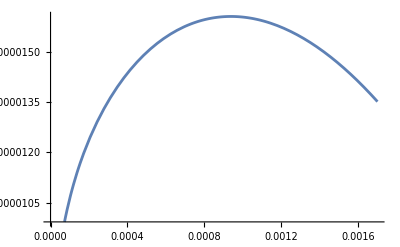

{rb→0.000937994}

```mathematica
e=3.0 10^6;u=50 10^3;ra=0.85;
r[rb_]:=π ((u/(e Log[ra/rb]))^2-rb^2)
Plot[r[rb],{rb,0,ra/500}]
FindRoot[D[r[rb], rb],{rb,1/10^6}]
```